```mathematica
Quit[]
```

```mathematica
<<"../../ltd_math_utils/LTDTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
allGraphs=importGraphs["./gammaddBar.qgr",sumIsoGraphs->True];
```

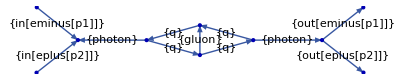

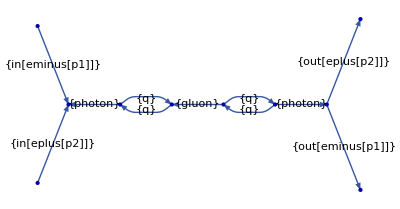

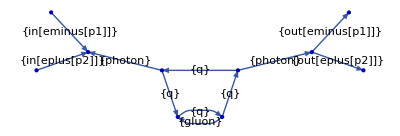

```mathematica
plotGraph[allGraphs,edgeLabels->{"particleType"}]
```

```mathematica
(* isomorphic graphs a summed in the importGraphs function (see numerator for last diagram is actually a sum)*)
allGraphs[[-1,"numerator"]]
```

-in[eminus[p1,-1]] in[eplus[p2,-3]] out[eminus[p1,-2]] out[eplus[p2,-4]] prop[gluon[k1+k2-p1-p2,{11,12}]] prop[photon[-p1-p2,{1,2}]] prop[photon[p1+p2,{3,4}]] prop[q[-k1,{5,6}]] prop[q[k2,{13,14}]] prop[q[-k1+p1+p2,{7,8}]] prop[q[-k1+p1+p2,{9,10}]] v[eplus[-p1,-2],photon[p1+p2,3],eminus[-p2,-4]] v[eplus[p2,-3],photon[-p1-p2,1],eminus[p1,-1]] v[qbar[k1,6],photon[-p1-p2,4],q[-k1+p1+p2,9]] v[qbar[-k2,14],gluon[k1+k2-p1-p2,11],q[-k1+p1+p2,7]] v[qbar[k1-p1-p2,8],photon[p1+p2,2],q[-k1,5]] v[qbar[k1-p1-p2,10],gluon[-k1-k2+p1+p2,12],q[k2,13]]-in[eminus[p1,-1]] in[eplus[p2,-3]] out[eminus[p1,-2]] out[eplus[p2,-4]] prop[gluon[k1+k2-p1-p2,{11,12}]] prop[photon[-p1-p2,{1,2}]] prop[photon[p1+p2,{3,4}]] prop[q[k1,{5,6}]] prop[q[-k2,{13,14}]] prop[q[k1-p1-p2,{7,8}]] prop[q[k1-p1-p2,{9,10}]] v[eplus[-p1,-2],photon[p1+p2,3],eminus[-p2,-4]] v[eplus[p2,-3],photon[-p1-p2,1],eminus[p1,-1]] v[qbar[-k1,6],photon[p1+p2,2],q[k1-p1-p2,7]] v[qbar[k2,14],gluon[-k1-k2+p1+p2,12],q[k1-p1-p2,9]] v[qbar[-k1+p1+p2,8],gluon[k1+k2-p1-p2,11],q[-k2,13]] v[qbar[-k1+p1+p2,10],photon[-p1-p2,4],q[k1,5]]

```mathematica
(* if we process the numerator, one diagram is killed since its 0 due to color *)
```

```mathematica
allGraphs=processNumerator[allGraphs,"./minFeynRulesQEDQCD.m",additionalRules->{SPD[p1,p1]->0}, symCoefficients->False,coeffFormat->"short",spinChainSimplify->True,spinSum->True];
```

```mathematica
((allGraphs[[1,"numerator"]]/.sp[x__]:>1//Expand)//DiracSimplify)[[1]]//FermionSpinSum
```

-512/9 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]]

## Plot graphs (for fresh start: rm -rf a.out *.qgr && gfortran qgraf-3.3.f && ./a.out )

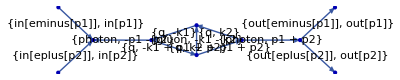

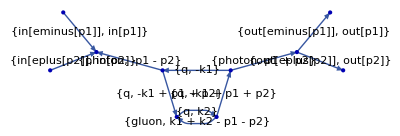

```mathematica
plotGraph[#,edgeLabels->{"particleType","momentumMap"},plotSize->Scaled[0.4]]&/@allGraphs;
```

## Create Cutkovsky-Cuts

```mathematica
<<"../../ltd_math_utils/LTDTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

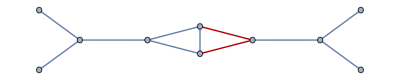

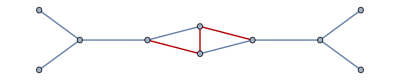

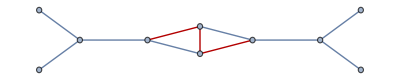

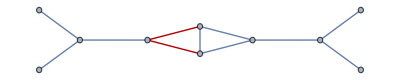

```mathematica
test=constructCuts[allGraphs[[1]]];
```

#### see the cut info and selfEnergy info

```mathematica
test
```

<|edges→{in[1]→v[1],in[2]→v[1],v[2]→out[1],v[2]→out[2],v[3]→v[1],v[4]→v[2],v[5]→v[3],v[3]→v[6],v[4]→v[5],v[6]→v[4],v[6]→v[5]},particleType→{in[eminus[p1]],in[eplus[p2]],out[eminus[p1]],out[eplus[p2]],photon,photon,q,q,q,q,gluon},momentumMap→{in[p1],in[p2],out[p1],out[p2],-p1-p2,p1+p2,-k1,-k1+p1+p2,k2,k2+p1+p2,-k1-k2},numerator→-(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]]^2 Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]]^2 Pair[Momentum[k2,D],Momentum[p1,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]]^2 Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]]^2 Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]]^2 Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]]^2 Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(3 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(512 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(3 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(3 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(3 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(1024 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(3 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(1024 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(256 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p1,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(2048 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(1024 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(128 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]]^2)/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] Pair[Momentum[p2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(256 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] Pair[Momentum[p2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(1024 CA CF ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]] Pair[Momentum[p2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])+(512 CA CF D ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]] Pair[Momentum[p2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2])-(64 CA CF D^2 ee^4 gs^2 ii^13 Pair[Momentum[k1,D],Momentum[k2,D]] Pair[Momentum[p1,D],Momentum[p2,D]] Pair[Momentum[p2,D],Momentum[p2,D]])/(9 sp[-p1-p2,-p1-p2] sp[p1+p2,p1+p2]),loopMomenta→{k1,k2},selfEnergieInfo→{<|problematicEdges→{},seDiagrams→{}|>,<|problematicEdges→{},seDiagrams→{}|>,<|problematicEdges→{},seDiagrams→{}|>,<|problematicEdges→{},seDiagrams→{}|>},cutDiagInfo→{{left,left,right,right,left,right,left,left,cut,cut,left},{left,left,right,right,left,right,cut,left,right,cut,cut},{left,left,right,right,left,right,left,cut,cut,right,cut},{left,left,right,right,left,right,cut,cut,right,right,right}}|>

```mathematica
test[["cutDiagInfo"]]//TableForm
```

left | left | right | right | left | right | left | left | cut | cut | left
left | left | right | right | left | right | cut | left | right | cut | cut
left | left | right | right | left | right | left | cut | cut | right | cut
left | left | right | right | left | right | cut | cut | right | right | right